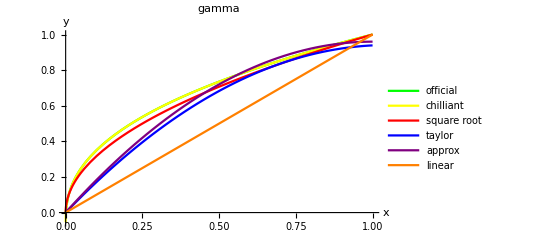

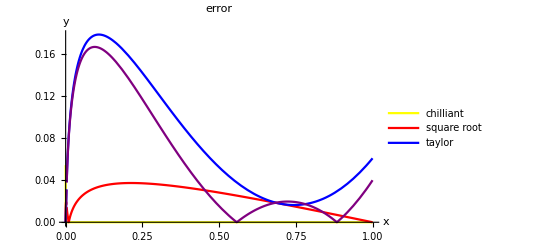

5.83868

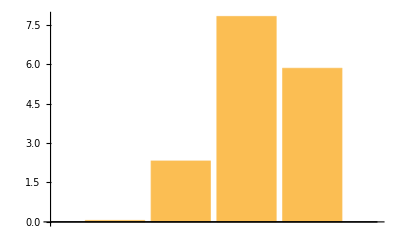

```mathematica
chilliantGamma[x_] := 1.055 * x^(1.0/2.4)-0.055
officialGamma[x_] := Piecewise[{{12.92 * x, x <= 0.0031308},{chilliantGamma[x],  x > 0.0031308}}]
sqrtGamma[x_] :=Sqrt[x] 
taylorGamma[x_]:= x *(-0.85373472095 *x +1.79284291400159)
approxGamma[x_] := x*(-0.96x+1.92)
linearGamma[x_] := x

llofficialGamma := LineLegend[{Green},{"official"}]
llchilliantGamma := LineLegend[{Yellow}, {"chilliant"}]
llsqrtGamma:= LineLegend[{Red},{"square root"}]
lltaylorGamma:= LineLegend[{Blue},{"taylor"}]
llapproxGamma := LineLegend[{Purple},{"approx"}]
lllinearGamma := LineLegend[{Orange}, {"linear"}]

Plot[
{officialGamma[x],chilliantGamma[x],sqrtGamma[x],taylorGamma[x], approxGamma[x], linearGamma[x]},
{x,0,1}, 
AxesLabel->{x,y},
PlotLabel->"gamma",
PlotStyle-> Thread[{Thick,{Green,Yellow, Red, Blue, Purple, Orange}}] ,
PlotLegends -> Framed[Column[{llofficialGamma, llchilliantGamma, llsqrtGamma, lltaylorGamma, llapproxGamma, lllinearGamma}]]
]

Plot[
{{Abs[officialGamma[x] - chilliantGamma[x]]},
{Abs[officialGamma[x] - sqrtGamma[x]]},
{Abs[officialGamma[x] - taylorGamma[x]]},
{Abs[officialGamma[x] - approxGamma[x]] }},
{x,0,1},
AxesLabel->{x,y},
PlotLabel->"error",
PlotStyle-> Thread[{Thick,{Yellow, Red, Blue, Purple}}] ,
PlotLegends -> Framed[Column[{llchilliantGamma,llsqrtGamma, lltaylorGamma, llapproxGamma}]]
]

errorChiliant := Sum[Abs[officialGamma[x] - chilliantGamma[x]],{ x, 0, 1, 0.01}]
errorSqrt := Sum[Abs[officialGamma[x] - sqrtGamma[x]],{ x, 0, 1, 0.01}]
errorTaylor := Sum[Abs[officialGamma[x] - taylorGamma[x]],{ x, 0, 1, 0.01}]
errorApprox = Sum[Abs[officialGamma[x] - approxGamma[x]],{ x, 0, 1, 0.01}]

BarChart[{errorChiliant,errorSqrt, errorTaylor, errorApprox}]
```

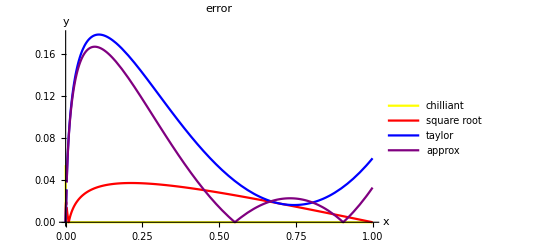

-Graphics-

```mathematica
3
```

3